## Problem Set 1

This assignment is to help you get started with basic Mathematica including useful functions, and list operations, together with some simple examples relevant to neuron modeling.

Don’t be intimated by some of the apparently long exercises. The long ones have illustrative points and usually require less work. 

As you go along, make sure you expand all the cells so that you don’t miss something.

Evaluate: 2/3, 2./3, N[2/3],  5^3, 4*3, 4 3.0

Start with simple arithmetic. For example, type 5+7 in an input cell, and then hit the "enter" key (or “shift” AND “return” together). Note that if you try division, e.g. 2/3, you get the exact answer back. To get a decimal approximation, type N[2/3].

You can go back and select an expression by clicking on the brackets on the far right. These brackets serve to organize text and calculations into a Notebook with outlining features. You can group or ungroup cells for text, graphs, and expressions in various ways to present your calculations. Explore these options under Cell in the menu.  You can see the possible cell types under the Style menu.

```mathematica
2/3
2./3
N[2/3]
5^3
4*3
4 3.0
```

2/3

0.666667

0.666667

125

12

12.

Seems pretty dumb so far...but you can see that Mathematica's default handling of arithmetic can make a difference in the next examples.

Precision

a)  Calculate the square roots of: 12345678987654321 and 12345678987654321.0. 

b) Compare (2^.000000000001)^1000000000000 with (2^(1/1000000000000))^1000000000000

```mathematica
Sqrt[12345678987654321]
Sqrt[12345678987654321.0]
```

111111111

1.11111111×10^8

```mathematica
(2^.000000000001)^1000000000000 == (2^(1/1000000000000))^1000000000000
```

False

If you don't explicitly tell Mathematica that your expressions involve floating point numbers, it will treat the numbers as true integers. And in general, Mathematica will do symbolic processing as a default, and assume you want as general an answer as possible. Because symbolic processing demands considerably more computer resources than numerical processing, this results in annoying consequences, like slow or no response. So remember to include a decimal point somewhere, or use N[ ] to force a floating point representation, and consequently numerical computations.

Use Mathematica to calculate the logarithm of 256 to base 2

```mathematica
Log[2, 256]
```

8

What does the Random function do? NormalDistribution[]? RandomVariate[ ]?

```mathematica
? NormalDistribution
```

```mathematica
? RandomVariate
```

Mathematica has extensive and well-organized documentation rich with examples. But you can get a quick summary of what a function does with a ? in front of the function. Answer this question by simply trying ?.

Simple linear neuron. Define a function y[ ] that takes three inputs {x1,x2,x3} with weights {w1,w2,w3} = {-1,2,-1}. What is the output, y,  of this model neuron if the three inputs are: 6, 33, 19 spikes per second?

```mathematica
y[x1_, x2_, x3_] := -1 * x1 + 2 * x2 + -1 * x3;
Print["The output is: ",  y[6, 33, 19]]
```

The output is: 41

Define xv using :=, and xf using =

```mathematica
xv:=RandomInteger[10];
xf=RandomInteger[10];
```

a) Now evaluate xv and xf three times each and explain the difference between how the xv behaves as compared with xf.

```mathematica
{xv, xf}
{xv, xf}
{xv, xf}
```

{5,0}

{2,0}

{7,0}

Answer:
xv returns a (possibly different) random integer (in the inclusive range 0-10) every time its value is requested. On the other hand, after defining xf, it returns the same value every time it is used. 
This behavior arises due to the fact that “=” means “immediate assignment” and “:=” means “delayed assignment”.

xf is assigned with “=” (immediate assignment), so during the definition of xf, RandomInteger[10] is called a single time and its return value is stored in xf.
xv is assigned with “:=” (delayed assignment), so RandomInteger[10] is evaluated every time xv’s value is requested.

Now do the same thing by making a list of lists: {{xv,xf},{xv,xf},{xv,xf}}

```mathematica
{{xv,xf},{xv,xf},{xv,xf}}
```

{{2,0},{5,0},{6,0}}

b) Compare repeated evaluations of the above with repeated evaluations of the two expressions below.

```mathematica
y[xv,xv,xv]
y[xf,xf,xf]
```

2

0

Repeated evaluations of {{xv,xf},{xv,xf},{xv,xf}} yields a matrix where the right column is the same value each time (the value of xf), and the left column may be different random integers in the range (0 - 10) (the values of xv)

Repeated evaluations of y[xv, xv, xv] yields possibly different (and possibly nonzero) results each time. As xv was assigned w/ delayed assignment, y[xv, xv, xv] receives three possibly different inputs each time it is called.
y[xf, xf, xf] returns 0 every time. As xf was assigned w/ immediate assignment, y[xf, xf, xf] receives three identical inputs and (as we will see in the next question) thus returns 0.

a) Why does the above neuron model y[ ] always output 0 when the inputs all have the same value? b) Think of y[ ] as a discrete approximation to a second derivative operator in calculus. What family of polynomial functions (e.g. a + bx + cx^2 + dx^3 + ...) all give a constant output (=k) when you take a second derivative? One can think of this family of patterns as an equivalent class of inputs whose variations the neuron is "blind" to. This y[] model is a highly simplified (1D) model of a retinal ganglion cell showing lateral inhibition with balanced excitatory and inhibitory inputs.

a) Why does the above neuron model y[ ] always output 0 when the inputs all have the same value? 
In short, when the inputs have the same value, the terms cancel out.
Simple proof: 
Assume x1 == x2 == x3 == some constant k.
y is by definition -1 * x1 + 2 * x2 + -1 * x3
	== -k + 2k - k
	== 0
b) Think of y[ ] as a discrete approximation to a second derivative operator in calculus. What family of polynomial functions (e.g. a + bx + cx^2 + dx^3 + ...) all give a constant output (=k) when you take a second derivative?
All quadratic functions have a constant second derivative.
That is:
y = ax^2 + bx + c, where a, b, c are constants
y’’ = 2a

Estimate the linear regime of a model neuron with the logistic sigmoid non-linearity squash[]

Some behavioral functions can be understood based on operating near the linear regime of non-linear neurons (e.g. some kinds of sensory transduction); however when embedded in a network consisting of many inter-connected neurons, the non-linear regime of neurons provides additional computational power.  We can approximate the linear range as the distance between the two inflection points of the first derivative of squash[]. Try executing and show the results, and estimate the range:

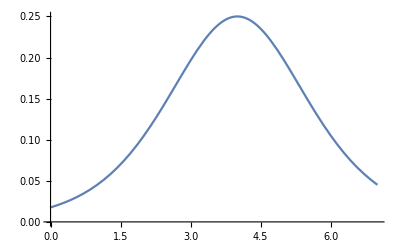

```mathematica
squash[x_]:=1/(1+Exp[-x+4]);
Plot[squash'[x],{x,0,7}]
```

Mathematica provides functions such as NSolve[] to automatically solve equations. Replace the ? with the appropriate expression to output the approximate linear range.

```mathematica
eq=D[1/(1+Exp[-x+4]),{x,3}];
NSolve[eq==0,x,Reals]
```

{{x→2.68304},{x→5.31696}}

Finding the linear operating range of a non-linear system is the same solution that audio engineers seek when designing a distortion-free amplifier.

Fourier analysis of a non-linear neuron’s response

Given a real neuron with an unknown point function, a time-honored way to empirically evaluate its degree of non-linearity is to use sine-wave inputs in time and/or space (e.g. as used in many studies of auditory and visual neurons). Suppose that a single model neuron below is stimulated with a scalar input that varies sinusoidally with time: amp*Cos[2*Pi*2.0*t]+offset;. The first panel of the plot below shows the output of the neuron as a function of time, the second panel shows the amplitude spectrum of the neuron’s “distorted” output, and the third panel shows the amplitude spectrum of the input. From the third panel you can see that the undistorted signal spectrum has peak frequency at  21 = 1+20 (and 101-20=81)(zero frequency starts at 1) . Distortion products are frequencies in the amplitude spectrum of the output that are distinct from that of the input frequency. For example, a squaring non-linearity produces frequency doubling--try executing TrigReduce[Cos[f]*Cos[f]];  For small input amplitudes away from the linear regime, the logistic sigmoid is approximately square-like. A type of neuron found in early cortex are complex cells, which have been modeled with a half-squaring operation.

Set the offset = 4.0. Approximately what is the amplitude range where the power at the harmonic frequency (near 40) approaches 10% of that of the fundamental at 20?

```mathematica
freq=20.0;
input[t_,amp_,offset_]:=amp*Cos[2*Pi*freq*t]+offset;
Manipulate[GraphicsRow[{Plot[squash[input[t,amp,offset]],{t,-.25,.25},PlotRange->{-1,1.5}],ListPlot[Abs[Fourier[Table[squash[input[t/100,amp,offset]],{t,1,100}]]],Joined->True,PlotRange->3.],ListPlot[Abs[Fourier[Table[input[t/100,amp,offset],{t,1,100}]]],Joined->True,PlotRange->2.0]}],{amp,.1,3},{{offset,4.0},-1,10}]
```

When amp is around 2 (or greater, kind of), the power at the harmonic frequency (near 40) approaches 10% of that of the fundamental at 20. Although it is kind of hard to tell just from visual inspection.

Define a new version of the squash function, squash2[x,λ], to include a steepness term λ, and whose values, like the logistic function, continue to range between 0 and 1. Then combine Plot[] with Manipulate[] to control  λ. The parameter λ provides a convenient way to change the neurons in a model from threshold logic units (that output near 0 or 1) to ones with a large linear regime. We’ll see this later in the course when we study Hopfield nets.

First use the prefix “?” to check the definition of the squash function already defined above:

```mathematica
?squash
```

```mathematica
squash2[x_,λ_]:=squash[x*λ]
```

```mathematica
Manipulate[
	Plot[squash2[x,λ], {x, -5, 10},PlotRange->{0,1.1}],{{λ,2},0.5,10}
]
```

Mathematica supplies a built-in “step function” called UnitStep[x]. Show UnitStep[x] and squash2[x,λ] on the same plot.

```mathematica
Manipulate[
	Plot[{squash2[x,λ], UnitStep[x]},{x,-5,10},PlotRange->{0,1.1}],{{λ,2},0.5,10}
]
```

Use a 3D graphics plot function to visualize a visual neuron’s two-dimensional receptive field

We sometimes want to visualize the effective weights (synaptic or other) of a model neuron. A plot of the weights shows how much to weight to multiply an the activity of input pattern at various locations (or times).  Many neurons in the visual cortex have 2D spatial pattern of weights, based on light intensity inputs,  that are modeled by a gaussian windowed sinusoid called a “gabor” function. The positive and negative weights represent excitatory and inhibitory influences. Here’s the equation that represents how such a neuron would weight light falling on various x-y positions of its receptive field:

-Graphics-

```mathematica
ZZZ[x_,y_, a_, b_] := Exp[-1*(x^2)-1*(y^2)]*Sin[a*x+b*y]
```

```mathematica
Manipulate[Plot3D[ZZZ[x, y, a, b],{x,-2,2},{y,-2,2},PlotRange->{-2,2}, ImageSize->Tiny],{a,1,6},{b,1,6}]
```

Lists, ListPlot[], and a preview of pattern classification based on vector representations of features

a) Suppose each instance of a category of patterns, that we’ll call “A”, has 2 features, such as brightness and size. Think of a feature as being represented by a dimension. How “much” of each of the features of A is represented by a pair of numbers {x,y}, x for how bright, and y for how big. And similarly for a second category, “B”. 

A particular “instance”, say the first, is then represented by a pair of feature values {x_1,y_1}. Suppose we have 3 instances for each category. Here are two lists in Mathematica list format:

```mathematica
A = {{0,1},{1,1.5},{1.7,1.6}};
B = {{.5,1.1},{1,3.},{2,3.5}};
```

Find and use the Mathematica function to return the number of rows and columns of list A. Hint: the function name begins with D. This function and similar versions in any scientific programming language gets used a lot.

Use ListPlot[ ] to plot A and B on the same graph. If you do it right, the A and B points will be automatically color coded.

Bring up Mathematica’s Drawing Tools from the Graphics menu. Use the straight line tool to try to draw a line between the instances of A and B. 

Are the classes linearly separable?

```mathematica
Dimensions[A]
Dimensions[B]
```

{3,2}

{3,2}

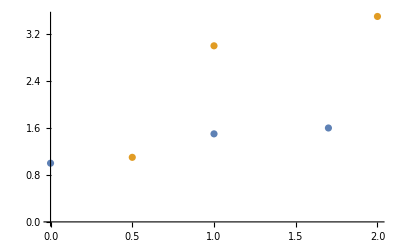

```mathematica
ListPlot[{A, B}]
```

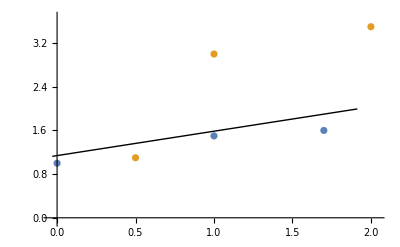

-Graphics-

The classes are not linearly separable

Associations as lists of rules mapping Keys to Values. Mathematica has database structures, like Python Dictionaries, that are useful for handling large datasets. We’ll use associations later in the course to organize training sets for machine learning. In Mathematica associations are based on lists of rules, e.g. {{0,1}→”A”,...}.

Combine A and B into a single Association with the 2D feature vectors as Keys, and the labels as Values. For example: {{0,1}→”A”,{.5,1.1}→”B” }. Then use Keys[] and Values[] to select the features and labels separately.

```mathematica
ass = AssociationMap[x |->"A", A];
assB = AssociationMap[x|->"B", B];
AssociateTo[ass, assB];

ass
```

<|{0,1}→A,{1,1.5}→A,{1.7,1.6}→A,{0.5,1.1}→B,{1,3.}→B,{2,3.5}→B|>

```mathematica
Keys[ass]
Values[ass]
```

{{0,1},{1,1.5},{1.7,1.6},{0.5,1.1},{1,3.},{2,3.5}}

{A,A,A,B,B,B}

Basic list construction and list/matrix manipulations

```mathematica
SeedRandom[0] (*Makes the random sampling deterministic--so we repeat with the same numbers*)
W = Table[RandomVariate[DiscreteUniformDistribution[{-4,4}]],{i,1,5},{j,1,4}]
```

RandomGeneratorState[…]

{{3,-4,4,-2},{-3,1,4,-4},{2,3,-2,-3},{-4,2,-3,-2},{4,2,1,1}}

Use Dimensions[] to find the dimensions of W. Note that Dimensions can be used as an operator, (@) 
as a function ([ ]), or post-hoc (//):

```mathematica
Dimensions[W]
```

{5,4}

Print out W in MatrixForm, e.g. using MatrixForm@W

```mathematica
MatrixForm@W
```

(3 | -4 | 4 | -2
-3 | 1 | 4 | -4
2 | 3 | -2 | -3
-4 | 2 | -3 | -2
4 | 2 | 1 | 1)

Use Mathematica’s slicing syntax, W[[row#,;;]] or W[[;;,col#]]to access the third row, and then second column of W

```mathematica
W[[3,;;]]
W[[;;,2]]
```

{2,3,-2,-3}

{-4,1,3,2,2}

Show the transpose of W in MatrixForm

```mathematica
MatrixForm@Transpose[W]
```

(3 | -3 | 2 | -4 | 4
-4 | 1 | 3 | 2 | 2
4 | 4 | -2 | -3 | 1
-2 | -4 | -3 | -2 | 1)

Show first three rows, just column 1:

```mathematica
W[[1;;3,1]]
```

{3,-3,2}

Show first row, just column elements 2 through 3:

```mathematica
W[[1,2;;3]]
```

{-4,4}

Replace the element in the 4th column and 2nd row of W with Pi as shown:

(2. | 1. | -2. | 3.
3. | 1. | -2. | π
4. | 6. | 5. | -3.
1. | -2. | 2. | 1.
3. | -3. | -22. | 1.)

```mathematica
W[[2,4]] = Pi;
MatrixForm@W
```

(3 | -4 | 4 | -2
-3 | 1 | 4 | π
2 | 3 | -2 | -3
-4 | 2 | -3 | -2
4 | 2 | 1 | 1)

Compare: {x1,x2,x3} {x1,x2,x3},  {x1,x2,x3}*{x1,x2,x3}, {x1,x2,x3}^2, {x1,x2,x3}.{x1,x2,x3}. In particular, note the difference between * and .

```mathematica
Clear[x1,x2,x3] (*First use clear because x1, x2, x3 were defined earlier in a different context*)
{x1,x2,x3} {x1,x2,x3}
{x1,x2,x3}*{x1,x2,x3}
{x1,x2,x3}^2
{x1,x2,x3}.{x1,x2,x3}
```

{x1^2,x2^2,x3^2}

{x1^2,x2^2,x3^2}

{x1^2,x2^2,x3^2}

x1^2+x2^2+x3^2

The first three result in element wise squaring, the last one is a dot product.

Map[ ]

Map[ ] is useful for quickly applying a function over a list. Define a reLU function: If[#>0,#,0]&, and map it over each element of W from the earlier exercise. Note that because W is a list of lists, you will have to map the function at the second level. Note  the syntax for the pure function definition ( If[#>0,#,0]& ), and also the /@ shorthand for Map.

```mathematica
reLU := If[# > 0, #, 0]&;
MatrixForm[Map[reLU, W, {2}]]
```

(3 | 0 | 4 | 0
0 | 1 | 4 | π
2 | 3 | 0 | 0
0 | 2 | 0 | 0
4 | 2 | 1 | 1)

Exercise: Simple non-linear neuron to compute the AND function

Using McCullochPitts[a, b, t], find a threshold value that will enable a McCulloch-Pitts neuron to realize the And[] function whose truth table is shown below.

```mathematica
truthtable=Flatten[Table[{a,b,And[a==1,b==1]},{a,0,1},{b,0,1}],1];
TableForm[truthtable,TableHeadings->{{},{"a", "b","c"}}]
```

| a | b | c
 | 0 | 0 | False
 | 0 | 1 | False
 | 1 | 0 | False
 | 1 | 1 | True

Print out the table. It should look like:

| a | b | c
 | 0 | 0 | 0
 | 0 | 1 | 0
 | 1 | 0 | 0
 | 1 | 1 | 1

```mathematica
McCullochPitts[a_,b_,t_]:=If[a+b≥t,1,0];
t = 2;
truthtable=Flatten[Table[{a,b,McCullochPitts[a, b, t]},{a,0,1},{b,0,1}],1];
TableForm[truthtable,TableHeadings->{{},{"a", "b","c"}}]
```

| a | b | c
 | 0 | 0 | 0
 | 0 | 1 | 0
 | 1 | 0 | 0
 | 1 | 1 | 1

Note how simple multiplication computes AND: Flatten[Table[{a,b,a * b},{a,0,1},{b,0,1}],1]. Further, with a point saturation function addition computes an OR: Flatten[Table[{a,b,myunitstep[a + b]},{a,0,1},{b,0,1}],1]; with myunitstep[x_]:=If[x≤0,0,1].

Execute and plot the truth tables for these two functions.

Later we will see one way in which a class of deep convolutional networks can be built using “AND-like” and “OR-like” neurons with continuous rather than binary outputs.

```mathematica
truthtable =Flatten[Table[{a,b,a*b},{a,0,1},{b,0,1}],1];
TableForm[truthtable,TableHeadings->{{},{"a", "b","c"}}]
```

| a | b | c
 | 0 | 0 | 0
 | 0 | 1 | 0
 | 1 | 0 | 0
 | 1 | 1 | 1

```mathematica
myunitstep[x_]:=If[x≤0,0,1];
truthtable=Flatten[Table[{a,b,myunitstep[a+b]},{a,0,1},{b,0,1}],1];
TableForm[truthtable,TableHeadings->{{},{"a", "b","c"}}]
```

| a | b | c
 | 0 | 0 | 0
 | 0 | 1 | 1
 | 1 | 0 | 1
 | 1 | 1 | 1